```mathematica
kb = 1.38*10^(-23);
h= 6.62* 10^(-34);
hbar = h/ 2 / 3.141;
micro = 10^(-6);
nano = 10^(-9);
giga = 10^9;
Tc = 7.2;
Δ0 = 3.528/2 * Tc*kb;
ωd = 296 * kb/hbar;
Δ[T_] :=Block[{z=Log[1.13 * hbar* ωd/kb/Tc], b=hbar ωd/2/kb},
Return[FindRoot[NIntegrate[Tanh[b/T*Sqrt[ϵ^2+x^2]]/Sqrt[ϵ^2 + x^2], {ϵ, 0, 1}, AccuracyGoal->2], -z, {x, 0.01, 0.1}][[1,2]]*hbar*ωd]];
Plot[Δ[x]/ Δ0, {x, 0.1, 7}]
```

FindRoot::fdss: Search specification -z should be a list with 1 to 5 elements.

General::stop: Further output of FindRoot :: fdss will be suppressed during this calculation.

-Graphics-

2.2345×10^-22 Tanh[1.74 √(-1+9.2/T)]

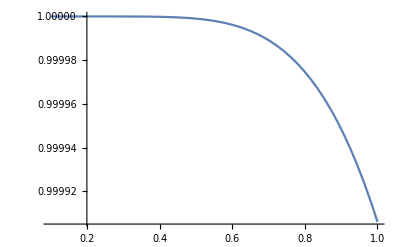

```mathematica
δ[T_]= 1.76 kb*Tc*Tanh[1.74*Sqrt[(Tc/T)-1] ]
Plot[ Tanh[1.74*Sqrt[(Tc/T)-1] ],{T, 0.1, 1.0} ]
```